```mathematica
Quit
```

Here Alex is set as reference surface and Sophie is the target surface .

```mathematica
SetDirectory[NotebookDirectory[]];
```

Read in mat file

```mathematica
Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/BaseSurface-Robot/OutputForLibigl/Mesh3/Robot_Mesh3_FaceRemesh.csv","Elements"]
```

{Data,Dataset,Dimensions,Grid,MaxColumnCount,RawData,RowCount,Summary}

The original meshes

```mathematica
FaceRef=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/BaseSurface-Robot/OutputForLibigl/Mesh3/Robot_Mesh3_FaceRemesh.csv","Data"];
```

```mathematica
FaceTar=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/TargetSurface-Sophie/OutputForLibigl/Mesh3/Sophie_Mesh3_FaceRemesh.csv","Data"];
```

```mathematica
VerticeRef=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/BaseSurface-Robot/OutputForLibigl/Mesh3/Robot_Mesh3_VerticeRemesh.csv","Data"];
VerticeTar=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/TargetSurface-Sophie/OutputForLibigl/Mesh3/Sophie_Mesh3_VerticeRemesh.csv","Data"];
```

```mathematica
Dimensions[FaceRef]
```

{16030,3}

```mathematica
Dimensions[VerticeRef]
```

{8150,3}

The parameterization results

```mathematica
UVRef=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/BaseSurface-Robot/OutputForLibigl/Mesh3/Robot_Mesh3_UVRemesh.csv","Data"];
UVTar=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/TargetSurface-Sophie/OutputForLibigl/Mesh3/Sophie_Mesh3_UVRemesh.csv","Data"];
```

Data check

```mathematica
If[FaceRef==FaceTar&&Dimensions[VerticeRef]==Dimensions[VerticeTar]&&UVRef==UVTar,"Pass","Data error"]
```

Pass

If pass

```mathematica
UV=UVRef;
Face=FaceRef;
```

The principal directions and curvatures of the reference surface

```mathematica
PD1Ref=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/BaseSurface-Robot/OutputForLibigl/Mesh3/Robot_Mesh3_PD1.txt","Data"];
PD2Ref=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/BaseSurface-Robot/OutputForLibigl/Mesh3/Robot_Mesh3_PD2.txt","Data"];
k1Ref=Flatten[Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/BaseSurface-Robot/OutputForLibigl/Mesh3/Robot_Mesh3_k1.txt","Data"]];
k2Ref=Flatten[Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/BaseSurface-Robot/OutputForLibigl/Mesh3/Robot_Mesh3_k2.txt","Data"]];
```

The principal directions and curvatures of the target surface

```mathematica
PD1Tar=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/TargetSurface-Sophie/OutputForLibigl/Mesh3/Sophie_Mesh3_PD1.txt","Data"];
PD2Tar=Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/TargetSurface-Sophie/OutputForLibigl/Mesh3/Sophie_Mesh3_PD2.txt","Data"];
k1Tar=Flatten[Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/TargetSurface-Sophie/OutputForLibigl/Mesh3/Sophie_Mesh3_k1.txt","Data"]];
k2Tar=Flatten[Import["D:/OneDrive - mail.scut.edu.cn/0 GrowOfSoftMatter/MathematicaCode/20230907GeneralShapeControl/UV网格重划分/TargetSurface-Sophie/OutputForLibigl/Mesh3/Sophie_Mesh3_k2.txt","Data"]];
```

```mathematica
nNodes=Dimensions[VerticeRef][[1]]
nFaces=Dimensions[Face][[1]]
```

8150

16030

计算混合积

```mathematica
MixProd=Table[({UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],1.0}).({UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],1.0}×{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],1.0}),{n,1,nFaces}];
```

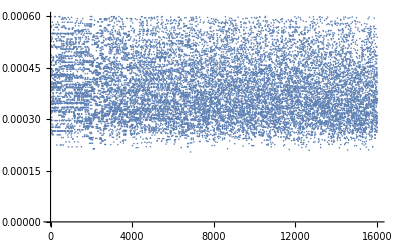

```mathematica
ListPlot[MixProd,PlotRange->All]
```

```mathematica
ii=1;Tabii={};While[ii≤ nFaces,If[MixProd[[ii]]< 0,AppendTo[Tabii,ii]];ii++];
```

```mathematica
Tabii
```

{}

```mathematica
Table[{{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,1]],3]]},{VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,2]],3]]},{VerticeRef[[Face[[n,3]],1]],VerticeRef[[Face[[n,3]],2]],VerticeRef[[Face[[n,3]],3]]}},{n,1,nFaces}];
ModelRef=Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
Table[{{VerticeTar[[Face[[n,1]],1]],VerticeTar[[Face[[n,1]],2]],VerticeTar[[Face[[n,1]],3]]},{VerticeTar[[Face[[n,2]],1]],VerticeTar[[Face[[n,2]],2]],VerticeTar[[Face[[n,2]],3]]},{VerticeTar[[Face[[n,3]],1]],VerticeTar[[Face[[n,3]],2]],VerticeTar[[Face[[n,3]],3]]}},{n,1,nFaces}];
ModelTar=Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
Show[ModelRef,ModelTar]
```

-Graphics3D-

```mathematica
Table[{{UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],0},{UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],0},{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],0}},{n,1,nFaces}];
UVPlane=Graphics3D[{Directive[RGBColor[0.618,0.618,1],Opacity[0.5]],Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
Show[ModelRef,UVPlane,ModelTar]
```

-Graphics3D-

compute the linear parametric equation for each face based on the formulations below
-Graphics-

{K11, K12, K13, K14}

```mathematica
MatK1Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,3]],1]],1/3(VerticeRef[[Face[[n,1]],1]]+VerticeRef[[Face[[n,2]],1]]+VerticeRef[[Face[[n,3]],1]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.216742,-0.870106,0.188588},{1.,-0.188533,-0.870106,0.164044},{1.,-0.202638,-0.852282,0.172704},{1.,-0.202638,-0.864165,0.175112}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,0.371611,-0.136284,-0.0506447},{1.,0.353767,-0.125383,-0.0443563},{1.,0.353766,-0.147184,-0.0520685},{1.,0.359715,-0.136283,-0.0490232}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K21, K22, K23}

```mathematica
MatK2Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,3]],2]],1/3(VerticeRef[[Face[[n,1]],2]]+VerticeRef[[Face[[n,2]],2]]+VerticeRef[[Face[[n,3]],2]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.216742,-0.870106,0.188588},{1.,-0.188533,-0.870106,0.164044},{1.,-0.202638,-0.852282,0.172704},{1.,-0.202638,-0.864165,0.175112}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,0.371611,-0.136284,-0.0506447},{1.,0.353767,-0.125383,-0.0443563},{1.,0.353766,-0.147184,-0.0520685},{1.,0.359715,-0.136283,-0.0490232}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K31, K32, K33}

```mathematica
MatK3Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],3]],VerticeRef[[Face[[n,2]],3]],VerticeRef[[Face[[n,3]],3]],1/3(VerticeRef[[Face[[n,1]],3]]+VerticeRef[[Face[[n,2]],3]]+VerticeRef[[Face[[n,3]],3]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.216742,-0.870106,0.188588},{1.,-0.188533,-0.870106,0.164044},{1.,-0.202638,-0.852282,0.172704},{1.,-0.202638,-0.864165,0.175112}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,0.371611,-0.136284,-0.0506447},{1.,0.353767,-0.125383,-0.0443563},{1.,0.353766,-0.147184,-0.0520685},{1.,0.359715,-0.136283,-0.0490232}} 构成的 Inverse 的结果可能包含明显的数值错误.

Check...

```mathematica
(*ListPlot[Table[MatK1Ref[[n,1]]+MatK1Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK1Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK1Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],1]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK2Ref[[n,1]]+MatK2Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK2Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK2Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],2]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK3Ref[[n,1]]+MatK3Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK3Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK3Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],3]],{n,1,nFaces}],PlotRange->All]*)
```

Check passed...

compute the coefficients of the element-wise first fundamental form.
-Graphics-
-Graphics-

尝试用计数，在节点处求和，求平均的思路解决

For each element, calculate {E, F, G}, count how many times a node is called, then calculate the average .

```mathematica
TmprX=Table[{0,0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nFaces,j=1;While[j<=3,TmprX[[Face[[i,j]]]]=TmprX[[Face[[i,j]]]]+{(MatK1Ref[[i,2]]+MatK1Ref[[i,4]]*UV[[Face[[i,j]],2]]),(MatK2Ref[[i,2]]+MatK2Ref[[i,4]]*UV[[Face[[i,j]],2]]),(MatK3Ref[[i,2]]+MatK3Ref[[i,4]]*UV[[Face[[i,j]],2]]),1};j++];i++]
```

```mathematica
TmprY=Table[{0,0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nFaces,j=1;While[j<=3,TmprY[[Face[[i,j]]]]=TmprY[[Face[[i,j]]]]+{MatK1Ref[[i,3]]+MatK1Ref[[i,4]]*UV[[Face[[i,j]],1]],MatK2Ref[[i,3]]+MatK2Ref[[i,4]]*UV[[Face[[i,j]],1]],MatK3Ref[[i,3]]+MatK3Ref[[i,4]]*UV[[Face[[i,j]],1]],1};j++];i++]
```

```mathematica
rXRef=Table[{TmprX[[n,1]]/TmprX[[n,4]],TmprX[[n,2]]/TmprX[[n,4]],TmprX[[n,3]]/TmprX[[n,4]]},{n,1,nNodes}];
rYRef=Table[{TmprY[[n,1]]/TmprY[[n,4]],TmprY[[n,2]]/TmprY[[n,4]],TmprY[[n,3]]/TmprY[[n,4]]},{n,1,nNodes}];
```

```mathematica
EERef=Table[rXRef[[n]].rXRef[[n]],{n,1,nNodes}];
```

```mathematica
FFRef=Table[rXRef[[n]].rYRef[[n]],{n,1,nNodes}];
```

```mathematica
GGRef=Table[rYRef[[n]].rYRef[[n]],{n,1,nNodes}];
```

检查 EFG

```mathematica
Table[{UV[[n,1]],UV[[n,2]],EERef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],FFRef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],GGRef[[n]]},{n,1,nNodes}];
EFGPlotRef=ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

compute the linear parametric equation for each face based on the formulations below
-Graphics-

{K11, K12, K13, K14}

```mathematica
MatK1Tar=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeTar[[Face[[n,1]],1]],VerticeTar[[Face[[n,2]],1]],VerticeTar[[Face[[n,3]],1]],1/3(VerticeTar[[Face[[n,1]],1]]+VerticeTar[[Face[[n,2]],1]]+VerticeTar[[Face[[n,3]],1]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.216742,-0.870106,0.188588},{1.,-0.188533,-0.870106,0.164044},{1.,-0.202638,-0.852282,0.172704},{1.,-0.202638,-0.864165,0.175112}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,0.371611,-0.136284,-0.0506447},{1.,0.353767,-0.125383,-0.0443563},{1.,0.353766,-0.147184,-0.0520685},{1.,0.359715,-0.136283,-0.0490232}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K21, K22, K23}

```mathematica
MatK2Tar=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeTar[[Face[[n,1]],2]],VerticeTar[[Face[[n,2]],2]],VerticeTar[[Face[[n,3]],2]],1/3(VerticeTar[[Face[[n,1]],2]]+VerticeTar[[Face[[n,2]],2]]+VerticeTar[[Face[[n,3]],2]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.216742,-0.870106,0.188588},{1.,-0.188533,-0.870106,0.164044},{1.,-0.202638,-0.852282,0.172704},{1.,-0.202638,-0.864165,0.175112}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,0.371611,-0.136284,-0.0506447},{1.,0.353767,-0.125383,-0.0443563},{1.,0.353766,-0.147184,-0.0520685},{1.,0.359715,-0.136283,-0.0490232}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K31, K32, K33}

```mathematica
MatK3Tar=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeTar[[Face[[n,1]],3]],VerticeTar[[Face[[n,2]],3]],VerticeTar[[Face[[n,3]],3]],1/3(VerticeTar[[Face[[n,1]],3]]+VerticeTar[[Face[[n,2]],3]]+VerticeTar[[Face[[n,3]],3]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.216742,-0.870106,0.188588},{1.,-0.188533,-0.870106,0.164044},{1.,-0.202638,-0.852282,0.172704},{1.,-0.202638,-0.864165,0.175112}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,0.371611,-0.136284,-0.0506447},{1.,0.353767,-0.125383,-0.0443563},{1.,0.353766,-0.147184,-0.0520685},{1.,0.359715,-0.136283,-0.0490232}} 构成的 Inverse 的结果可能包含明显的数值错误.

Check...

```mathematica
(*ListPlot[Table[MatK1Tar[[n,1]]+MatK1Tar[[n,2]]*UV[[Face[[n,1]],1]]+MatK1Tar[[n,3]]*UV[[Face[[n,1]],2]]+MatK1Tar[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeTar[[Face[[n,1]],1]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK2Tar[[n,1]]+MatK2Tar[[n,2]]*UV[[Face[[n,1]],1]]+MatK2Tar[[n,3]]*UV[[Face[[n,1]],2]]+MatK2Tar[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeTar[[Face[[n,1]],2]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK3Tar[[n,1]]+MatK3Tar[[n,2]]*UV[[Face[[n,1]],1]]+MatK3Tar[[n,3]]*UV[[Face[[n,1]],2]]+MatK3Tar[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeTar[[Face[[n,1]],3]],{n,1,nFaces}],PlotRange->All]*)
```

Check passed...

compute the coefficients of the element-wise first fundamental form.
-Graphics-
-Graphics-

尝试用计数，在节点处求和，求平均的思路解决

For each element, calculate {E, F, G}, count how many times a node is called, then calculate the average .

```mathematica
TmprX=Table[{0,0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nFaces,j=1;While[j<=3,TmprX[[Face[[i,j]]]]=TmprX[[Face[[i,j]]]]+{(MatK1Tar[[i,2]]+MatK1Tar[[i,4]]*UV[[Face[[i,j]],2]]),(MatK2Tar[[i,2]]+MatK2Tar[[i,4]]*UV[[Face[[i,j]],2]]),(MatK3Tar[[i,2]]+MatK3Tar[[i,4]]*UV[[Face[[i,j]],2]]),1};j++];i++]
```

```mathematica
TmprY=Table[{0,0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nFaces,j=1;While[j<=3,TmprY[[Face[[i,j]]]]=TmprY[[Face[[i,j]]]]+{MatK1Tar[[i,3]]+MatK1Tar[[i,4]]*UV[[Face[[i,j]],1]],MatK2Tar[[i,3]]+MatK2Tar[[i,4]]*UV[[Face[[i,j]],1]],MatK3Tar[[i,3]]+MatK3Tar[[i,4]]*UV[[Face[[i,j]],1]],1};j++];i++]
```

```mathematica
rXTar=Table[{TmprX[[n,1]]/TmprX[[n,4]],TmprX[[n,2]]/TmprX[[n,4]],TmprX[[n,3]]/TmprX[[n,4]]},{n,1,nNodes}];
rYTar=Table[{TmprY[[n,1]]/TmprY[[n,4]],TmprY[[n,2]]/TmprY[[n,4]],TmprY[[n,3]]/TmprY[[n,4]]},{n,1,nNodes}];
```

```mathematica
EETar=Table[rXTar[[n]].rXTar[[n]],{n,1,nNodes}];
```

```mathematica
FFTar=Table[rXTar[[n]].rYTar[[n]],{n,1,nNodes}];
```

```mathematica
GGTar=Table[rYTar[[n]].rYTar[[n]],{n,1,nNodes}];
```

检查 EFG

```mathematica
Table[{UV[[n,1]],UV[[n,2]],EETar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],FFTar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],GGTar[[n]]},{n,1,nNodes}];
EFGPlotTar=ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

mathematic preliminaries
-Graphics-
α.β=(MG-NF)/(LF-ME), α=(PD1.ru)/(PD1.rv), β=(PD2.ru)/(PD2.rv)

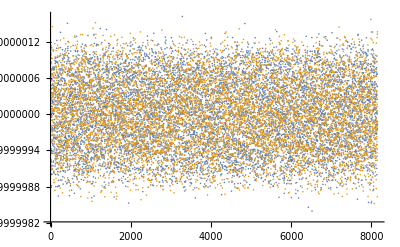

```mathematica
Table[PD1Ref[[n]].PD1Ref[[n]],{n,1,nNodes}];
Table[PD2Ref[[n]].PD2Ref[[n]],{n,1,nNodes}];
ListPlot[{%%,%},PlotRange->All]
```

从上图可见主方向已经单位化了，不满意可以再单位化一遍，接下来求解LMN

求解LMN with conformal mapping assumption

```mathematica
Solve[{Pk1+Pk2==(Lr+Nr)/Er,(*Pk1*Pk2==(-Mr^2+Lr Nr)/Er^2,*)α==-Mr/(Lr-Pk1 Er),β==-Mr/(Lr-Pk2 Er)},{Lr,Mr,Nr}];
FullSimplify[%]
```

{{Lr→(Er (Pk1 α-Pk2 β))/(α-β),Mr→(Er (-Pk1+Pk2) α β)/(α-β),Nr→(Er (Pk2 α-Pk1 β))/(α-β)}}

将解析解代入方程2，验证是否成立
Pk1*Pk2==(-Mr^2+Lr Nr)/Er^2，先计算右半边

```mathematica
(-Mr^2+Lr Nr)/Er^2/.{Lr->(Er (Pk1 α-Pk2 β))/(α-β),Mr->(Er (-Pk1+Pk2) α β)/(α-β),Nr->(Er (Pk2 α-Pk1 β))/(α-β)}//Simplify
Simplify[%,α β==-1]
```

(-Pk1^2 α β (1+α β)-Pk2^2 α β (1+α β)+Pk1 Pk2 (β^2+α^2 (1+2 β^2)))/(α-β)^2

Pk1 Pk2

求解LMN in general case

```mathematica
Solve[{Pk1+Pk2==(Lr Gr-2Mr Fr+Nr Er)/(Er Gr-Fr^2),(*Pk1*Pk2==(Lr Nr-Mr^2)/(Er Gr-Fr^2),*)α==-(Mr-Pk1 Fr)/(Lr-Pk1 Er),β==-(Mr-Pk2 Fr)/(Lr-Pk2 Er)},{Lr,Mr,Nr}]//FullSimplify
```

{{Lr→(Fr Pk1-Fr Pk2+Er Pk1 α-Er Pk2 β)/(α-β),Mr→(Er (-Pk1+Pk2) α β+Fr (Pk2 α-Pk1 β))/(α-β),Nr→(-Fr^2 (Pk1-Pk2) (α+β)+Er Gr (Pk2 α-Pk1 β)-Fr (Pk1-Pk2) (Gr+2 Er α β))/(Er (α-β))}}

```mathematica
αRef=Table[(PD1Ref[[n]].rXRef[[n]])/(PD1Ref[[n]].rYRef[[n]]) ,{n,1,nNodes}];
βRef=Table[(PD2Ref[[n]].rXRef[[n]])/(PD2Ref[[n]].rYRef[[n]]),{n,1,nNodes}];
```

检查Libigl计算的主方向

```mathematica
Table[{UV[[n,1]],UV[[n,2]],αRef[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%}]
```

-Graphics3D-

```mathematica
Table[{UV[[n,1]],UV[[n,2]],βRef[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%}]
```

-Graphics3D-

检查Libigl计算的主曲率

```mathematica
Table[{UV[[n,1]],UV[[n,2]],k1Ref[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],k2Ref[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%%,%},PlotRange->All]
```

-Graphics3D-

计算LMN

```mathematica
LLRef=Flatten[Table[1/(αRef[[n]]-βRef[[n]]) (FFRef[[n]] k1Ref[[n]]-FFRef[[n]] k2Ref[[n]]+EERef[[n]] k1Ref[[n]] αRef[[n]]-EERef[[n]] k2Ref[[n]] βRef[[n]]),{n,1,nNodes}]];
```

```mathematica
MMRef=Flatten[Table[1/(αRef[[n]]-βRef[[n]])(EERef[[n]] (-k1Ref[[n]]+k2Ref[[n]]) αRef[[n]] βRef[[n]]+FFRef[[n]] (k2Ref[[n]] αRef[[n]]-k1Ref[[n]] βRef[[n]])),{n,1,nNodes}]];
```

```mathematica
NNRef=Flatten[Table[1/(EERef[[n]] (αRef[[n]]-βRef[[n]]))(-(FFRef[[n]])^2 (k1Ref[[n]]-k2Ref[[n]]) (αRef[[n]]+βRef[[n]])+EERef[[n]] GGRef[[n]] (k2Ref[[n]] αRef[[n]]-k1Ref[[n]] βRef[[n]])-FFRef[[n]] (k1Ref[[n]]-k2Ref[[n]]) (GGRef[[n]]+2 EERef[[n]] αRef[[n]] βRef[[n]])),{n,1,nNodes}]];
```

```mathematica
DatumPlane=Graphics3D[{Gray,Opacity[0.6],Polygon[{{-1,-1,0},{-1,1,0},{1,1,0},{1,-1,0}}]}];
```

检查四条方程中，没有使用的第二条方程 （高斯曲率） 是否满足
Pk1*Pk2==(Lr Nr-Mr^2)/(Er Gr-Fr^2)

```mathematica
CheckEq2=Flatten[Table[k1Ref[[n]]*k2Ref[[n]]-(LLRef[[n]] NNRef[[n]]-MMRef[[n]]^2)/(EERef[[n]] GGRef[[n]]-FFRef[[n]]^2),{n,1,nNodes}]];
Table[{UV[[n,1]],UV[[n,2]],CheckEq2[[n]]},{n,1,nNodes}];
Show[ListPointPlot3D[%],DatumPlane]
```

-Graphics3D-

方程不太满足，公式无误，矫正主方向无改善，有可能是三角形网格离散化，还有libigl计算误差导致的

检查 LMN

```mathematica
Table[{UV[[n,1]],UV[[n,2]],LLRef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],MMRef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],NNRef[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics3D-

mathematic preliminaries
-Graphics-
α.β=(MG-NF)/(LF-ME), α=(PD1.ru)/(PD1.rv), β=(PD2.ru)/(PD2.rv)

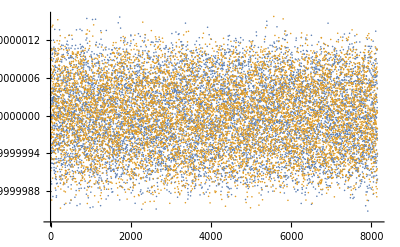

```mathematica
Table[PD1Tar[[n]].PD1Tar[[n]],{n,1,nNodes}];
Table[PD2Tar[[n]].PD2Tar[[n]],{n,1,nNodes}];
ListPlot[{%%,%},PlotRange->All]
```

从上图可见主方向已经单位化了，不满意可以再单位化一遍，接下来求解LMN

求解LMN with conformal mapping assumption

```mathematica
Solve[{Pk1+Pk2==(Lr+Nr)/Er,(*Pk1*Pk2==(-Mr^2+Lr Nr)/Er^2,*)α==-Mr/(Lr-Pk1 Er),β==-Mr/(Lr-Pk2 Er)},{Lr,Mr,Nr}];
FullSimplify[%]
```

{{Lr→(Er (Pk1 α-Pk2 β))/(α-β),Mr→(Er (-Pk1+Pk2) α β)/(α-β),Nr→(Er (Pk2 α-Pk1 β))/(α-β)}}

将解析解代入方程2，验证是否成立
Pk1*Pk2==(-Mr^2+Lr Nr)/Er^2，先计算右半边

```mathematica
(-Mr^2+Lr Nr)/Er^2/.{Lr->(Er (Pk1 α-Pk2 β))/(α-β),Mr->(Er (-Pk1+Pk2) α β)/(α-β),Nr->(Er (Pk2 α-Pk1 β))/(α-β)}//Simplify
Simplify[%,α β==-1]
```

(-Pk1^2 α β (1+α β)-Pk2^2 α β (1+α β)+Pk1 Pk2 (β^2+α^2 (1+2 β^2)))/(α-β)^2

Pk1 Pk2

求解LMN in general case

```mathematica
Solve[{Pk1+Pk2==(Lr Gr-2Mr Fr+Nr Er)/(Er Gr-Fr^2),(*Pk1*Pk2==(Lr Nr-Mr^2)/(Er Gr-Fr^2),*)α==-(Mr-Pk1 Fr)/(Lr-Pk1 Er),β==-(Mr-Pk2 Fr)/(Lr-Pk2 Er)},{Lr,Mr,Nr}]//FullSimplify
```

{{Lr→(Fr Pk1-Fr Pk2+Er Pk1 α-Er Pk2 β)/(α-β),Mr→(Er (-Pk1+Pk2) α β+Fr (Pk2 α-Pk1 β))/(α-β),Nr→(-Fr^2 (Pk1-Pk2) (α+β)+Er Gr (Pk2 α-Pk1 β)-Fr (Pk1-Pk2) (Gr+2 Er α β))/(Er (α-β))}}

```mathematica
αTar=Table[(PD1Tar[[n]].rXTar[[n]])/(PD1Tar[[n]].rYTar[[n]]) ,{n,1,nNodes}];
βTar=Table[(PD2Tar[[n]].rXTar[[n]])/(PD2Tar[[n]].rYTar[[n]]),{n,1,nNodes}];
```

检查Libigl计算的主方向

```mathematica
Table[{UV[[n,1]],UV[[n,2]],αTar[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%}]
```

-Graphics3D-

```mathematica
Table[{UV[[n,1]],UV[[n,2]],βTar[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%}]
```

-Graphics3D-

检查Libigl计算的主曲率

```mathematica
Table[{UV[[n,1]],UV[[n,2]],k1Tar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],k2Tar[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%%,%},PlotRange->All]
```

-Graphics3D-

计算LMN

```mathematica
LLTar=Flatten[Table[1/(αTar[[n]]-βTar[[n]]) (FFTar[[n]] k1Tar[[n]]-FFTar[[n]] k2Tar[[n]]+EETar[[n]] k1Tar[[n]] αTar[[n]]-EETar[[n]] k2Tar[[n]] βTar[[n]]),{n,1,nNodes}]];
```

```mathematica
MMTar=Flatten[Table[1/(αTar[[n]]-βTar[[n]])(EETar[[n]] (-k1Tar[[n]]+k2Tar[[n]]) αTar[[n]] βTar[[n]]+FFTar[[n]] (k2Tar[[n]] αTar[[n]]-k1Tar[[n]] βTar[[n]])),{n,1,nNodes}]];
```

```mathematica
NNTar=Flatten[Table[1/(EETar[[n]] (αTar[[n]]-βTar[[n]]))(-(FFTar[[n]])^2 (k1Tar[[n]]-k2Tar[[n]]) (αTar[[n]]+βTar[[n]])+EETar[[n]] GGTar[[n]] (k2Tar[[n]] αTar[[n]]-k1Tar[[n]] βTar[[n]])-FFTar[[n]] (k1Tar[[n]]-k2Tar[[n]]) (GGTar[[n]]+2 EETar[[n]] αTar[[n]] βTar[[n]])),{n,1,nNodes}]];
```

```mathematica
DatumPlane=Graphics3D[{Gray,Opacity[0.6],Polygon[{{-1,-1,0},{-1,1,0},{1,1,0},{1,-1,0}}]}];
```

检查四条方程中，没有使用的第二条方程 （高斯曲率） 是否满足
Pk1*Pk2==(Lr Nr-Mr^2)/(Er Gr-Fr^2)

```mathematica
CheckEq2=Flatten[Table[k1Tar[[n]]*k2Tar[[n]]-(LLTar[[n]] NNTar[[n]]-MMTar[[n]]^2)/(EETar[[n]] GGTar[[n]]-FFTar[[n]]^2),{n,1,nNodes}]];
Table[{UV[[n,1]],UV[[n,2]],CheckEq2[[n]]},{n,1,nNodes}];
Show[ListPointPlot3D[%],DatumPlane]
```

-Graphics3D-

方程不太满足，公式无误，矫正主方向无改善，有可能是三角形网格离散化，还有libigl计算误差导致的

检查 LMN

```mathematica
Table[{UV[[n,1]],UV[[n,2]],LLTar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],MMTar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],NNTar[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics3D-

三维模型的生成
先计算各节点的单位法向量n

```mathematica
InverseVectorFlag=-1;
```

```mathematica
VertornRef=InverseVectorFlag*Table[(rXRef[[n]]×rYRef[[n]])/(√((rXRef[[n]]×rYRef[[n]]).(rXRef[[n]]×rYRef[[n]]))),{n,1,nNodes}];
```

```mathematica
VertornTar=Table[(rXTar[[n]]×rYTar[[n]])/(√((rXTar[[n]]×rYTar[[n]]).(rXTar[[n]]×rYTar[[n]]))),{n,1,nNodes}];
```

```mathematica
HeadRad=0.01;
TubeRad=0.002;
nLen=0.05;
```

```mathematica
Table[{{VerticeRef[[n,1]],VerticeRef[[n,2]],VerticeRef[[n,3]]},{VerticeRef[[n,1]],VerticeRef[[n,2]],VerticeRef[[n,3]]}+nLen{VertornRef[[n,1]],VertornRef[[n,2]],VertornRef[[n,3]]}},{n,1,nNodes}];
nPlot=Graphics3D[{Red,Arrowheads[HeadRad],Arrow[Tube[%,TubeRad] ]}];
Show[nPlot,ModelRef]
```

-Graphics3D-

```mathematica
Table[{{VerticeTar[[n,1]],VerticeTar[[n,2]],VerticeTar[[n,3]]},{VerticeTar[[n,1]],VerticeTar[[n,2]],VerticeTar[[n,3]]}+nLen{VertornTar[[n,1]],VertornTar[[n,2]],VertornTar[[n,3]]}},{n,1,nNodes}];
nPlot=Graphics3D[{Red,Arrowheads[HeadRad],Arrow[Tube[%,TubeRad] ]}];
Show[nPlot,ModelTar]
```

-Graphics3D-

Verification passed

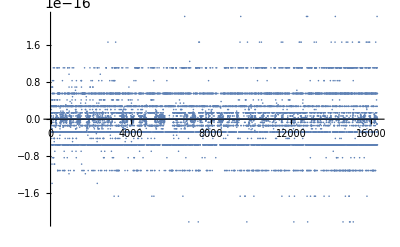

```mathematica
Flatten[Table[{VertornRef[[n]].rXRef[[n]],VertornRef[[n]].rYRef[[n]]},{n,1,nNodes}]];
ListPlot[%,PlotRange->All]
```

将节点沿法向平移，number of layers is 3

```mathematica
Th=0.01*1/3((Max[VerticeRef[[All,1]]]-Min[VerticeRef[[All,1]]])+(Max[VerticeRef[[All,2]]]-Min[VerticeRef[[All,2]]])+(Max[VerticeRef[[All,3]]]-Min[VerticeRef[[All,3]]]))
```

0.0123601

```mathematica
NodesL1=Table[VerticeRef[[n]]-Th/2 VertornRef[[n]],{n,1,nNodes}];
NodesL2=VerticeRef;
NodesL3=Table[VerticeRef[[n]]+Th/2 VertornRef[[n]],{n,1,nNodes}];
```

```mathematica
Table[{{NodesL1[[Face[[n,1]],1]],NodesL1[[Face[[n,1]],2]],NodesL1[[Face[[n,1]],3]]},{NodesL1[[Face[[n,2]],1]],NodesL1[[Face[[n,2]],2]],NodesL1[[Face[[n,2]],3]]},{NodesL1[[Face[[n,3]],1]],NodesL1[[Face[[n,3]],2]],NodesL1[[Face[[n,3]],3]]}},{n,1,nFaces}];
Layer1Plot=Graphics3D[Polygon[%]];
Table[{{NodesL2[[Face[[n,1]],1]],NodesL2[[Face[[n,1]],2]],NodesL2[[Face[[n,1]],3]]},{NodesL2[[Face[[n,2]],1]],NodesL2[[Face[[n,2]],2]],NodesL2[[Face[[n,2]],3]]},{NodesL2[[Face[[n,3]],1]],NodesL2[[Face[[n,3]],2]],NodesL2[[Face[[n,3]],3]]}},{n,1,nFaces}];
Layer2Plot=Graphics3D[Polygon[%]];
Table[{{NodesL3[[Face[[n,1]],1]],NodesL3[[Face[[n,1]],2]],NodesL3[[Face[[n,1]],3]]},{NodesL3[[Face[[n,2]],1]],NodesL3[[Face[[n,2]],2]],NodesL3[[Face[[n,2]],3]]},{NodesL3[[Face[[n,3]],1]],NodesL3[[Face[[n,3]],2]],NodesL3[[Face[[n,3]],3]]}},{n,1,nFaces}];
Layer3Plot=Graphics3D[Polygon[%]];
```

```mathematica
Show[Layer3Plot,Layer1Plot,PlotRange->All]
```

-Graphics3D-

曲面交叉了怎么办？让abaqus判断吧。

Output {a1,a2,a3} {b1,b2,b3} for CAE
g1 = {a1, a2, a3};
g2 = {b1, b2, b3};

```mathematica
a1MiddleRef=Table[1/3(rXRef[[Face[[n,1]],1]]+rXRef[[Face[[n,2]],1]]+rXRef[[Face[[n,3]],1]]),{n,1,nFaces}];
a2MiddleRef=Table[1/3(rXRef[[Face[[n,1]],2]]+rXRef[[Face[[n,2]],2]]+rXRef[[Face[[n,3]],2]]),{n,1,nFaces}];a3MiddleRef=Table[1/3(rXRef[[Face[[n,1]],3]]+rXRef[[Face[[n,2]],3]]+rXRef[[Face[[n,3]],3]]),{n,1,nFaces}];
```

```mathematica
b1MiddleRef=Table[1/3(rYRef[[Face[[n,1]],1]]+rYRef[[Face[[n,2]],1]]+rYRef[[Face[[n,3]],1]]),{n,1,nFaces}];
b2MiddleRef=Table[1/3(rYRef[[Face[[n,1]],2]]+rYRef[[Face[[n,2]],2]]+rYRef[[Face[[n,3]],2]]),{n,1,nFaces}];b3MiddleRef=Table[1/3(rYRef[[Face[[n,1]],3]]+rYRef[[Face[[n,2]],3]]+rYRef[[Face[[n,3]],3]]),{n,1,nFaces}];
```

```mathematica
Export["OutputForCAE/a1.csv",N[a1MiddleRef]];
Export["OutputForCAE/a2.csv",N[a2MiddleRef]];
Export["OutputForCAE/a3.csv",N[a3MiddleRef]];
Export["OutputForCAE/b1.csv",N[b1MiddleRef]];
Export["OutputForCAE/b2.csv",N[b2MiddleRef]];
Export["OutputForCAE/b3.csv",N[b3MiddleRef]];
```

Output nodes for CAE

```mathematica
NodesLayer1=Table[{n,NodesL1[[n,1]],NodesL1[[n,2]],NodesL1[[n,3]]},{n,1,nNodes}];
NodesLayer2=Table[{n+nNodes,NodesL2[[n,1]],NodesL2[[n,2]],NodesL2[[n,3]]},{n,1,nNodes}];
NodesLayer3=Table[{n+2nNodes,NodesL3[[n,1]],NodesL3[[n,2]],NodesL3[[n,3]]},{n,1,nNodes}];
```

```mathematica
OptNodes=Join[NodesLayer1,NodesLayer2,NodesLayer3];
```

```mathematica
Dimensions[OptNodes]
```

{24450,4}

Element is from bottom to top

```mathematica
(*EleLayer1=Table[{ii,Face[[ii,1]],Face[[ii,2]],Face[[ii,3]],Face[[ii,1]]+nNodes,Face[[ii,2]]+nNodes,Face[[ii,3]]+nNodes},{ii,1,nFaces}];

EleLayer2=Table[{ii+nFaces,Face[[ii,1]]+nNodes,Face[[ii,2]]+nNodes,Face[[ii,3]]+nNodes,Face[[ii,1]]+2nNodes,Face[[ii,2]]+2nNodes,Face[[ii,3]]+2nNodes},{ii,1,nFaces}];*)
```

```mathematica
EleLayer1=Table[{ii,Face[[ii,1]],Face[[ii,3]],Face[[ii,2]],Face[[ii,1]]+nNodes,Face[[ii,3]]+nNodes,Face[[ii,2]]+nNodes},{ii,1,nFaces}];

EleLayer2=Table[{ii+nFaces,Face[[ii,1]]+nNodes,Face[[ii,3]]+nNodes,Face[[ii,2]]+nNodes,Face[[ii,1]]+2nNodes,Face[[ii,3]]+2nNodes,Face[[ii,2]]+2nNodes},{ii,1,nFaces}];
```

先做两层

```mathematica
OptEleNumber=Join[EleLayer1,EleLayer2];
```

Boundary Conditions

```mathematica
TopMid=0;
```

```mathematica
BotMid=0;
```

```mathematica
BotRight=0;
```

```mathematica
nFaces*2
```

32060

```mathematica
Export["OutputForCAE/Mma128140Element.csv",Join[{{"nodes  ",3nNodes}},OptNodes,{{ }},{{"elements  ",2nFaces}},OptEleNumber,{{ }},{{"*Nset, nset=BotNode, generate"},{1,nNodes,1}},{{"*Nset, nset=TopNode, generate"},{1+2nNodes,3nNodes,1}},{{"*Nset, nset=BotMid"},{BotMid}},{{"*Nset, nset=BotRight"},{BotRight}},{{"*Nset, nset=TopMid"},{TopMid}}]];
```

Calculate growth function

{DetGTmp1, λ10Tmp1, λ20Tmp1, λs0Tmp1}

```mathematica
GrowthFunTmp1=Table[{((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-1+(((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFTar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] (-FFTar[[n]]^2 FFRef[[n]]+EETar[[n]] FFRef[[n]] GGTar[[n]]+FFTar[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) ((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])^2)))/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))),((-((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]])))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) √((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-EETar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),(((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFRef[[n]] (FFTar[[n]] FFRef[[n]] GGTar[[n]]+EERef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]))+EERef[[n]] FFTar[[n]] GGTar[[n]] GGRef[[n]])+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) √((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))))/((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),-√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))))},{n,1,nNodes}];
```

{DetGTmp2, λ10Tmp2, λ20Tmp2, λs0Tmp2}

```mathematica
GrowthFunTmp2=Table[{((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-1+(((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFTar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] (-FFTar[[n]]^2 FFRef[[n]]+EETar[[n]] FFRef[[n]] GGTar[[n]]+FFTar[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) ((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])^2)))/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))),(((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) √((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-EETar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),((-((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFRef[[n]] (FFTar[[n]] FFRef[[n]] GGTar[[n]]+EERef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]))+EERef[[n]] FFTar[[n]] GGTar[[n]] GGRef[[n]]))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) √((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))))/((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))))},{n,1,nNodes}];
```

{DetGTmp3, λ10Tmp3, λ20Tmp3, λs0Tmp3}

```mathematica
GrowthFunTmp3=Table[{((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-1-(((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFTar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] (-FFTar[[n]]^2 FFRef[[n]]+EETar[[n]] FFRef[[n]] GGTar[[n]]+FFTar[[n]] GGTar[[n]] GGRef[[n]])))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])^2)))/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))),(√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))) (-((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]])))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-EETar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),(√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))) ((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFRef[[n]] (FFTar[[n]] FFRef[[n]] GGTar[[n]]+EERef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]))+EERef[[n]] FFTar[[n]] GGTar[[n]] GGRef[[n]])-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),-√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))))},{n,1,nNodes}];
```

{DetGTmp4, λ10Tmp4, λ20Tmp4, λs0Tmp4}

```mathematica
GrowthFunTmp4=Table[{((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-1-(((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFTar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] (-FFTar[[n]]^2 FFRef[[n]]+EETar[[n]] FFRef[[n]] GGTar[[n]]+FFTar[[n]] GGTar[[n]] GGRef[[n]])))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])^2)))/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))),(√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))) ((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-EETar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),(√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))) (-((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFRef[[n]] (FFTar[[n]] FFRef[[n]] GGTar[[n]]+EERef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]))+EERef[[n]] FFTar[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))))},{n,1,nNodes}];
```

```mathematica
LambdaZ0=Table[{0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nNodes,If[GrowthFunTmp4[[i,1]]>0&&GrowthFunTmp4[[i,2]]>0&&GrowthFunTmp4[[i,3]]>0,LambdaZ0[[i,1]]=GrowthFunTmp4[[i,2]];LambdaZ0[[i,2]]=GrowthFunTmp4[[i,3]];LambdaZ0[[i,3]]=GrowthFunTmp4[[i,4]];];i++]
```

```mathematica
i=1;While[i<=nNodes,If[GrowthFunTmp3[[i,1]]>0&&GrowthFunTmp3[[i,2]]>0&&GrowthFunTmp3[[i,3]]>0,LambdaZ0[[i,1]]=GrowthFunTmp3[[i,2]];LambdaZ0[[i,2]]=GrowthFunTmp3[[i,3]];LambdaZ0[[i,3]]=GrowthFunTmp3[[i,4]];];i++]
```

```mathematica
i=1;While[i<=nNodes,If[GrowthFunTmp2[[i,1]]>0&&GrowthFunTmp2[[i,2]]>0&&GrowthFunTmp2[[i,3]]>0,LambdaZ0[[i,1]]=GrowthFunTmp2[[i,2]];LambdaZ0[[i,2]]=GrowthFunTmp2[[i,3]];LambdaZ0[[i,3]]=GrowthFunTmp2[[i,4]];];i++]
```

```mathematica
i=1;While[i<=nNodes,If[GrowthFunTmp1[[i,1]]>0&&GrowthFunTmp1[[i,2]]>0&&GrowthFunTmp1[[i,3]]>0,LambdaZ0[[i,1]]=GrowthFunTmp1[[i,2]];LambdaZ0[[i,2]]=GrowthFunTmp1[[i,3]];LambdaZ0[[i,3]]=GrowthFunTmp1[[i,4]];];i++]
```

```mathematica
λ10=Table[LambdaZ0[[n,1]],{n,1,nNodes}];
λ20=Table[LambdaZ0[[n,2]],{n,1,nNodes}];
λs0=Table[LambdaZ0[[n,3]],{n,1,nNodes}];
```

这里加入判断，若生长函数λ0等于零，则上面的解不适用。
要换成别的解。

```mathematica
CountFail=0;
```

```mathematica
i=1;While[i<=nNodes,If[λ10[[i]]==0,λ10[[i]]=2.04;λ20[[i]]=1;λs0[[i]]=0;CountFail++];i++]
```

```mathematica
CountFail
```

0

```mathematica
λ11=Table[(-((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) GGRef[[n]] (-λ10[[n]] (GGTar[[n]] LLRef[[n]] λ10[[n]]-FFTar[[n]] MMRef[[n]] λ10[[n]]+EETar[[n]] LLRef[[n]] λ20[[n]])+(FFTar[[n]] LLRef[[n]]-EETar[[n]] MMRef[[n]]) λ10[[n]] λs0[[n]]+EETar[[n]] LLRef[[n]] λs0[[n]]^2))+FFRef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (-λ10[[n]] (GGTar[[n]] MMRef[[n]] λ10[[n]]-FFTar[[n]] NNRef[[n]] λ10[[n]]+FFTar[[n]] LLRef[[n]] λ20[[n]]+EETar[[n]] MMRef[[n]] λ20[[n]])-(GGTar[[n]] LLRef[[n]]-2 FFTar[[n]] MMRef[[n]]+EETar[[n]] NNRef[[n]]) λ10[[n]] λs0[[n]]+2 FFTar[[n]] LLRef[[n]] λs0[[n]]^2)+FFRef[[n]]^2 (-λ10[[n]] (GGTar[[n]]^2 LLTar[[n]] λ10[[n]]+FFTar[[n]]^2 (NNTar[[n]] λ10[[n]]-LLTar[[n]] λ20[[n]])+GGTar[[n]] (-2 FFTar[[n]] MMTar[[n]] λ10[[n]]+EETar[[n]] LLTar[[n]] λ20[[n]]))+2 (FFTar[[n]] GGTar[[n]] LLTar[[n]]-FFTar[[n]]^2 MMTar[[n]]-EETar[[n]] GGTar[[n]] MMTar[[n]]+EETar[[n]] FFTar[[n]] NNTar[[n]]) λ10[[n]] λs0[[n]]+(-2 FFTar[[n]]^2 LLTar[[n]]+2 EETar[[n]] FFTar[[n]] MMTar[[n]]+EETar[[n]] (GGTar[[n]] LLTar[[n]]-EETar[[n]] NNTar[[n]])) λs0[[n]]^2)+EERef[[n]] (λ10[[n]] (GGRef[[n]] (GGTar[[n]]^2 LLTar[[n]]-2 FFTar[[n]] GGTar[[n]] MMTar[[n]]+FFTar[[n]]^2 NNTar[[n]]) λ10[[n]]+(FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (-GGRef[[n]] LLTar[[n]]+FFTar[[n]] MMRef[[n]]) λ20[[n]])+(EETar[[n]] GGTar[[n]] (2 GGRef[[n]] MMTar[[n]]-GGTar[[n]] MMRef[[n]])+FFTar[[n]]^2 (2 GGRef[[n]] MMTar[[n]]+GGTar[[n]] MMRef[[n]])-2 FFTar[[n]] GGRef[[n]] (GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]])-FFTar[[n]]^3 NNRef[[n]]+EETar[[n]] FFTar[[n]] GGTar[[n]] NNRef[[n]]) λ10[[n]] λs0[[n]]+(-2 FFTar[[n]]^3 MMRef[[n]]+2 EETar[[n]] FFTar[[n]] (-GGRef[[n]] MMTar[[n]]+GGTar[[n]] MMRef[[n]])+FFTar[[n]]^2 (2 GGRef[[n]] LLTar[[n]]+EETar[[n]] NNRef[[n]])-EETar[[n]] (GGTar[[n]] GGRef[[n]] LLTar[[n]]-EETar[[n]] GGRef[[n]] NNTar[[n]]+EETar[[n]] GGTar[[n]] NNRef[[n]])) λs0[[n]]^2))/((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (-GGTar[[n]] λ10[[n]]-EETar[[n]] λ20[[n]]+2 FFTar[[n]] λs0[[n]])),{n,1,nNodes}]
```

```mathematica
λ21=Table[(-EETar[[n]] (-FFRef[[n]] GGTar[[n]] MMRef[[n]]+FFRef[[n]]^2 NNTar[[n]]-EERef[[n]] GGRef[[n]] NNTar[[n]]+EERef[[n]] GGTar[[n]] NNRef[[n]]) λ20[[n]] (GGTar[[n]] λ10[[n]]+EETar[[n]] λ20[[n]])+EETar[[n]] GGTar[[n]] (-2 FFRef[[n]]^2 MMTar[[n]]+2 EERef[[n]] GGRef[[n]] MMTar[[n]]-(EERef[[n]] GGTar[[n]]+EETar[[n]] GGRef[[n]]) MMRef[[n]]+FFRef[[n]] (GGTar[[n]] LLRef[[n]]+EETar[[n]] NNRef[[n]])) λ20[[n]] λs0[[n]]+GGTar[[n]] (EERef[[n]] GGTar[[n]] GGRef[[n]] LLTar[[n]]-EETar[[n]] GGTar[[n]] GGRef[[n]] LLRef[[n]]-EETar[[n]] EERef[[n]] GGRef[[n]] NNTar[[n]]+FFRef[[n]]^2 (-GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]])+EETar[[n]] EERef[[n]] GGTar[[n]] NNRef[[n]]) λs0[[n]]^2+FFTar[[n]]^3 (λ20[[n]] (GGRef[[n]] MMRef[[n]] λ10[[n]]-FFRef[[n]] NNRef[[n]] λ10[[n]]+FFRef[[n]] LLRef[[n]] λ20[[n]]-EERef[[n]] MMRef[[n]] λ20[[n]])-(GGRef[[n]] LLRef[[n]]-2 FFRef[[n]] MMRef[[n]]+EERef[[n]] NNRef[[n]]) λ20[[n]] λs0[[n]]+2 (-GGRef[[n]] MMRef[[n]]+FFRef[[n]] NNRef[[n]]) λs0[[n]]^2)+FFTar[[n]]^2 (EERef[[n]] λ20[[n]] (-GGRef[[n]] NNTar[[n]] λ10[[n]]+GGTar[[n]] NNRef[[n]] λ10[[n]]+GGRef[[n]] LLTar[[n]] λ20[[n]]+EETar[[n]] NNRef[[n]] λ20[[n]])+(2 EERef[[n]] GGRef[[n]] MMTar[[n]]+EERef[[n]] GGTar[[n]] MMRef[[n]]+EETar[[n]] GGRef[[n]] MMRef[[n]]) λ20[[n]] λs0[[n]]+(GGTar[[n]] GGRef[[n]] LLRef[[n]]+2 EERef[[n]] GGRef[[n]] NNTar[[n]]-EERef[[n]] GGTar[[n]] NNRef[[n]]) λs0[[n]]^2-FFRef[[n]] λ20[[n]] (GGTar[[n]] MMRef[[n]] λ10[[n]]+EETar[[n]] MMRef[[n]] λ20[[n]]+GGTar[[n]] LLRef[[n]] λs0[[n]]+EETar[[n]] NNRef[[n]] λs0[[n]])+FFRef[[n]]^2 (NNTar[[n]] λ10[[n]] λ20[[n]]-LLTar[[n]] λ20[[n]]^2-2 MMTar[[n]] λ20[[n]] λs0[[n]]-2 NNTar[[n]] λs0[[n]]^2))+FFTar[[n]] (2 GGTar[[n]] (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) λs0[[n]] (LLTar[[n]] λ20[[n]]+MMTar[[n]] λs0[[n]])+2 EETar[[n]] (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) λ20[[n]] (MMTar[[n]] λ20[[n]]+NNTar[[n]] λs0[[n]])+EETar[[n]] GGTar[[n]] (λ20[[n]] (-GGRef[[n]] MMRef[[n]] λ10[[n]]+FFRef[[n]] NNRef[[n]] λ10[[n]]-FFRef[[n]] LLRef[[n]] λ20[[n]]+EERef[[n]] MMRef[[n]] λ20[[n]])+(GGRef[[n]] LLRef[[n]]-2 FFRef[[n]] MMRef[[n]]+EERef[[n]] NNRef[[n]]) λ20[[n]] λs0[[n]]+2 (GGRef[[n]] MMRef[[n]]-FFRef[[n]] NNRef[[n]]) λs0[[n]]^2)))/((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (-GGTar[[n]] λ10[[n]]-EETar[[n]] λ20[[n]]+2 FFTar[[n]] λs0[[n]])),{n,1,nNodes}]
```

```mathematica
λs1=Table[(EETar[[n]] GGTar[[n]] (-2 FFRef[[n]]^2 MMTar[[n]]+2 EERef[[n]] GGRef[[n]] MMTar[[n]]-(EERef[[n]] GGTar[[n]]+EETar[[n]] GGRef[[n]]) MMRef[[n]]+FFRef[[n]] (GGTar[[n]] LLRef[[n]]+EETar[[n]] NNRef[[n]])) λ10[[n]] λ20[[n]]+(GGTar[[n]]^2 (-FFRef[[n]]^2 LLTar[[n]]+EERef[[n]] GGRef[[n]] LLTar[[n]]-EETar[[n]] GGRef[[n]] LLRef[[n]]+EETar[[n]] FFRef[[n]] MMRef[[n]]) λ10[[n]]+EETar[[n]]^2 (FFRef[[n]] GGTar[[n]] MMRef[[n]]-FFRef[[n]]^2 NNTar[[n]]+EERef[[n]] GGRef[[n]] NNTar[[n]]-EERef[[n]] GGTar[[n]] NNRef[[n]]) λ20[[n]]) λs0[[n]]+FFTar[[n]] ((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]]) λ10[[n]] λ20[[n]]+(GGTar[[n]] GGRef[[n]] (-2 EERef[[n]] MMTar[[n]]+EETar[[n]] MMRef[[n]]) λ10[[n]]+EETar[[n]] EERef[[n]] (-2 GGRef[[n]] MMTar[[n]]+GGTar[[n]] MMRef[[n]]) λ20[[n]]+2 FFRef[[n]]^2 MMTar[[n]] (GGTar[[n]] λ10[[n]]+EETar[[n]] λ20[[n]])-EETar[[n]] FFRef[[n]] GGTar[[n]] (NNRef[[n]] λ10[[n]]+LLRef[[n]] λ20[[n]])) λs0[[n]]+(EETar[[n]] GGTar[[n]] GGRef[[n]] LLRef[[n]]-2 EETar[[n]] FFRef[[n]] GGTar[[n]] MMRef[[n]]+FFRef[[n]]^2 (GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]])-EERef[[n]] GGRef[[n]] (GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]])+EETar[[n]] EERef[[n]] GGTar[[n]] NNRef[[n]]) λs0[[n]]^2)-FFTar[[n]]^3 λs0[[n]] (GGRef[[n]] (MMRef[[n]] λ10[[n]]+LLRef[[n]] λs0[[n]])-FFRef[[n]] (NNRef[[n]] λ10[[n]]+LLRef[[n]] λ20[[n]]+2 MMRef[[n]] λs0[[n]])+EERef[[n]] (MMRef[[n]] λ20[[n]]+NNRef[[n]] λs0[[n]]))+FFTar[[n]]^2 (EERef[[n]] GGTar[[n]] MMRef[[n]] λ10[[n]] λ20[[n]]+GGRef[[n]] λ10[[n]] (EETar[[n]] MMRef[[n]] λ20[[n]]+GGTar[[n]] LLRef[[n]] λs0[[n]])-FFRef[[n]]^2 λs0[[n]] (NNTar[[n]] λ10[[n]]+LLTar[[n]] λ20[[n]]+2 MMTar[[n]] λs0[[n]])+EERef[[n]] λs0[[n]] (EETar[[n]] NNRef[[n]] λ20[[n]]+GGRef[[n]] (NNTar[[n]] λ10[[n]]+LLTar[[n]] λ20[[n]]+2 MMTar[[n]] λs0[[n]]))-FFRef[[n]] (EETar[[n]] λ20[[n]] (NNRef[[n]] λ10[[n]]+MMRef[[n]] λs0[[n]])+GGTar[[n]] λ10[[n]] (LLRef[[n]] λ20[[n]]+MMRef[[n]] λs0[[n]]))))/((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (-GGTar[[n]] λ10[[n]]-EETar[[n]] λ20[[n]]+2 FFTar[[n]] λs0[[n]])),{n,1,nNodes}]
```

Convert growth functions from nodal to element - wise

```mathematica
λ10Middle=Table[1/3(λ10[[Face[[n,1]]]]+λ10[[Face[[n,2]]]]+λ10[[Face[[n,3]]]]),{n,1,nFaces}];
λ20Middle=Table[1/3(λ20[[Face[[n,1]]]]+λ20[[Face[[n,2]]]]+λ20[[Face[[n,3]]]]),{n,1,nFaces}];
λs0Middle=Table[1/3(λs0[[Face[[n,1]]]]+λs0[[Face[[n,2]]]]+λs0[[Face[[n,3]]]]),{n,1,nFaces}];
```

```mathematica
λ11Middle=Table[1/3(λ11[[Face[[n,1]]]]+λ11[[Face[[n,2]]]]+λ11[[Face[[n,3]]]]),{n,1,nFaces}];
λ21Middle=Table[1/3(λ21[[Face[[n,1]]]]+λ21[[Face[[n,2]]]]+λ21[[Face[[n,3]]]]),{n,1,nFaces}];
λs1Middle=Table[1/3(λs1[[Face[[n,1]]]]+λs1[[Face[[n,2]]]]+λs1[[Face[[n,3]]]]),{n,1,nFaces}];
```

```mathematica
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λ10Middle[[n]]},{n,1,nFaces}];
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λ20Middle[[n]]},{n,1,nFaces}];
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λs0Middle[[n]]},{n,1,nFaces}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics3D-

```mathematica
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λ11Middle[[n]]},{n,1,nFaces}];
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λ21Middle[[n]]},{n,1,nFaces}];
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λs1Middle[[n]]},{n,1,nFaces}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics3D-

为什么生长函数的Z阶会这么大

```mathematica
Export["OutputForCAE/Lambda10.csv",N[λ10Middle]];
Export["OutputForCAE/Lambda20.csv",N[λ20Middle]];
Export["OutputForCAE/Lambdas0.csv",N[λs0Middle]];
Export["OutputForCAE/Lambda11.csv",N[λ11Middle]];
Export["OutputForCAE/Lambda21.csv",N[λ21Middle]];
Export["OutputForCAE/Lambdas1.csv",N[λs1Middle]];
```

对比一下两个曲面的EFG和LMN

```mathematica
Table[{UV[[n,1]],UV[[n,2]],EETar[[n]]/EERef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],FFTar[[n]]/FFRef[[n]]+0.0001},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],GGTar[[n]]/GGRef[[n]]+0.0002},{n,1,nNodes}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

```mathematica
Table[{UV[[n,1]],UV[[n,2]],LLTar[[n]]/LLRef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],MMTar[[n]]/MMRef[[n]]+0.0001},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],NNTar[[n]]/NNRef[[n]]+0.0002},{n,1,nNodes}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-